```mathematica
h:=-f √(Ja Jb)Cos[ϕa-ϕb+2 δ/R]+δ/R(Ja-Jb)+1/2(p Ja^2+2 q Ja Jb+r Jb^2)-f1 Ja Jb (1+Cos[2ϕa-2ϕb+4 δ/R+α])
```

```mathematica
FullSimplify[-D[h,ϕa]]
```

-2 f1 Ja Jb Sin[α+(4 δ)/R+2 ϕa-2 ϕb]-f √(Ja Jb) Sin[(2 δ)/R+ϕa-ϕb]

```mathematica
FullSimplify[D[h,Ja]]
```

-f1 Jb+Ja p+Jb q+δ/R-f1 Jb Cos[α+(4 δ)/R+2 ϕa-2 ϕb]-(f Jb Cos[(2 δ)/R+ϕa-ϕb])/(2 √(Ja Jb))

```mathematica
FullSimplify[-D[h,ϕb]]
```

2 f1 Ja Jb Sin[α+(4 δ)/R+2 ϕa-2 ϕb]+f √(Ja Jb) Sin[(2 δ)/R+ϕa-ϕb]

```mathematica
FullSimplify[D[h,Jb]]
```

-f1 Ja+Ja q+Jb r-δ/R-f1 Ja Cos[α+(4 δ)/R+2 ϕa-2 ϕb]-(f Ja Cos[(2 δ)/R+ϕa-ϕb])/(2 √(Ja Jb))

```mathematica
hh=FullSimplify[h/.{Ja->(II+J)/2,Jb->(II-J)/2,ϕa->ϕb-(2 δ)/R+Φ}]
```

1/(8 R)(2 f1 (-II^2+J^2) R+(II+J) ((II+J) p+2 (II-J) q) R+(II-J)^2 r R+8 J δ-4 f √((II-J) (II+J)) R Cos[Φ]+2 f1 (-II^2+J^2) R Cos[α+2 Φ])

```mathematica
hhRound=Simplify[hh/.{δ->η Cos[Θ]}]
```

(2 f1 (-II^2+J^2) R+(II+J) ((II+J) p+2 (II-J) q) R+(II-J)^2 r R+8 J η Cos[Θ]-4 f √(II^2-J^2) R Cos[Φ]+2 f1 (-II^2+J^2) R Cos[α+2 Φ])/(8 R)

```mathematica
Jshtrich=FullSimplify[-D[hh,Φ]]
```

1/2 (-f √(II^2-J^2) Sin[Φ]+f1 (-II^2+J^2) Sin[α+2 Φ])

```mathematica
Jshtrich=1/2 (-f √((II-J) (II+J)) Sin[Φ]+f1 (-II^2+J^2)( Sin[α](1-2Sin[Φ]^2)+2cos[α]Sin[Φ]Sqrt[1-Sin[Φ]^2]));
```

```mathematica
Jshtrich=Jshtrich/.{Sin[Φ]->x}
```

1/2 (-f √((II-J) (II+J)) x+f1 (-II^2+J^2) (2 x √(1-x^2) cos[α]+(1-2 x^2) Sin[α]))

```mathematica
Solve[Jshtrich==0,x]
```

{{x→-(f √((II-J) (II+J)) (-4 II^2+4 J^2) Sin[α])/(4 f1 (4 II^4 cos[α]^2-8 II^2 J^2 cos[α]^2+4 J^4 cos[α]^2+4 II^4 Sin[α]^2-8 II^2 J^2 Sin[α]^2+4 J^4 Sin[α]^2))-1/2 √(f^2/(12 f1^2 (II^2-J^2) (cos[α]^2+Sin[α]^2))-(II^2 cos[α]^2)/(3 (II^2-J^2) (cos[α]^2+Sin[α]^2))+46+(2^(1/3) J^4 Sin[α]^4)/(3 (1)^2 1^2 (1)^(1/3))+((75+√(1^2+1))^(1/3))/(3 2^(1/3)))-1/2 √(-f^2/(12 f1^2 (II^2-J^2) (cos[α]^2+Sin[α]^2))+63)},{x→1},1,{x→-(f √1 1 Sin[α])/(4 f1 (1))+1/2 √1+1/2 √1}}
 |  |  |  |

```mathematica
Flatten[%28];
```

```mathematica
Φshtrich=FullSimplify[D[hh,J]]
```

1/4 (II p-II r+J (2 f1+p-2 q+r)+(4 δ)/R+(2 f J Cos[Φ])/(√((II-J) (II+J)))+2 f1 J Cos[α+2 Φ])

```mathematica
Φshtrich=1/4 (II p-II r+J (2 f1+p-2 q+r)+(4 δ)/R+(2 f J Sqrt[1-x^2])/(√((II-J) (II+J)))+2 f1 J (Cos[α](1-2x^2)-2Sin[α]x Sqrt[1-x^2]));
```

```mathematica
Simplify[Nsolve[Φshtrich/.{II->1,f->-0.2,f1->.5,R->1,p->-0.02,q->-0.5,r->0.02,%30[[1]],α->π/6},J]]
```

$Aborted

```mathematica
FullSimplify[D[hh,II]]
```

1/4 (-2 f1 II+J (p-r)+II (p+2 q+r)-(2 f II Cos[Φ])/(√((II-J) (II+J)))-2 f1 II Cos[α+2 Φ])

```mathematica
Manipulate[ContourPlot[hh/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07,α->αp},{Φ, -π,π},{J, -1, 1},Contours->10],{αp,0,4π}]
```

```mathematica
sol=Flatten[Solve[{Jshtrich==0,Φshtrich==0},{J,Φ}]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Eliminate[{ Jshtrich==0,Φshtrich==0}/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07},J]
```

(1089.+1320. Cos[α+2. Φ]+400. Cos[α+2. Φ]^2) Sin[Φ]^4+Cos[Φ] (-1320.-800. Cos[α+2. Φ]) Sin[Φ]^3 Sin[α+2. Φ]+(-26384.+400. Cos[Φ]^2-33000. Cos[α+2. Φ]-10000. Cos[α+2. Φ]^2) Sin[Φ]^2 Sin[α+2. Φ]^2+Cos[Φ] (33000.+20000. Cos[α+2. Φ]) Sin[Φ] Sin[α+2. Φ]^3==10000. Cos[Φ]^2 Sin[α+2. Φ]^4

```mathematica
solPlot=Flatten[Solve[Eliminate[{ Jshtrich==0,Φshtrich==0}/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07},J],Φ]];
```

$Aborted

```mathematica
Dimensions[solPlot]
```

{56}

```mathematica
Jplot={J/.{solPlot[[1]]},J/.{solPlot[[3]]},J/.{solPlot[[5]]},J/.{solPlot[[7]]},J/.{solPlot[[9]]},J/.{solPlot[[11]]},J/.{solPlot[[13]]},J/.{solPlot[[15]]},J/.{solPlot[[17]]},J/.{solPlot[[19]]},J/.{solPlot[[21]]},J/.{solPlot[[23]]},J/.{solPlot[[25]]},J/.{solPlot[[27]]},J/.{solPlot[[29]]},J/.{solPlot[[31]]},J/.{solPlot[[33]]},J/.{solPlot[[35]]},J/.{solPlot[[37]]},J/.{solPlot[[39]]},J/.{solPlot[[41]]},J/.{solPlot[[43]]},J/.{solPlot[[45]]},J/.{solPlot[[47]]},J/.{solPlot[[49]]},J/.{solPlot[[51]]},J/.{solPlot[[53]]},J/.{solPlot[[55]]}};
```

```mathematica
Φplot={Φ/.{solPlot[[2]]},Φ/.{solPlot[[4]]},Φ/.{solPlot[[6]]},Φ/.{solPlot[[8]]},Φ/.{solPlot[[10]]},Φ/.{solPlot[[12]]},Φ/.{solPlot[[14]]},Φ/.{solPlot[[16]]},Φ/.{solPlot[[18]]},Φ/.{solPlot[[20]]},Φ/.{solPlot[[22]]},Φ/.{solPlot[[24]]},Φ/.{solPlot[[26]]},Φ/.{solPlot[[28]]},Φ/.{solPlot[[30]]},Φ/.{solPlot[[32]]},Φ/.{solPlot[[34]]},Φ/.{solPlot[[36]]},Φ/.{solPlot[[38]]},Φ/.{solPlot[[40]]},Φ/.{solPlot[[42]]},Φ/.{solPlot[[44]]},Φ/.{solPlot[[46]]},Φ/.{solPlot[[48]]},Φ/.{solPlot[[50]]},Φ/.{solPlot[[52]]},Φ/.{solPlot[[54]]},Φ/.{solPlot[[56]]}};
```

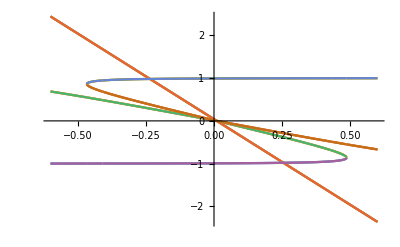

```mathematica
Plot[Jplot,{δ,-.6,.6}]
```

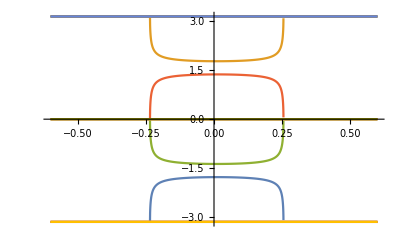

```mathematica
Plot[Φplot,{δ,-.6,.6}]
```

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→-0.943957-9.33782×10^-19 ⅈ,J→0.142438+1.47905×10^-17 ⅈ,J→0.348935-1.75238×10^-17 ⅈ,J→0.852584+3.66707×10^-18 ⅈ}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→-0.860094,J→0.834837,J→16.0126-10.0061 ⅈ,J→16.0126+10.0061 ⅈ}

```mathematica
ΦΦ=FullSimplify[D[hh,{Φ,2}]]
```

1/2 f √((II-J) (II+J)) Cos[Φ]+f1 (II-J) (II+J) Cos[2 Φ]

```mathematica
JJ = FullSimplify[D[hh,{J,2}]]
```

1/4 (2 f1+p-2 q+r+(2 f II^2 Cos[Φ])/((II-J) (II+J))^(3/2)+2 f1 Cos[2 Φ])

```mathematica
ΦJ=FullSimplify[D[D[hh,Φ],J]]
```

-(f J Sin[Φ])/(2 √((II-J) (II+J)))-f1 J Sin[2 Φ]

```mathematica
ΦΦ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0756148

```mathematica
JJ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.241302

```mathematica
ΦΦ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0550497

```mathematica
JJ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.609426

```mathematica
_________________________________________________without α
```

```mathematica
h:=-f √(Ja Jb)Cos[ϕa-ϕb+2 δ/R]+δ/R(Ja-Jb)+1/2(p Ja^2+2 q Ja Jb+r Jb^2)-f1 Ja Jb (1+Cos[2ϕa-2ϕb+4 δ/R])
```

```mathematica
FullSimplify[-D[h,ϕa]]
```

-(f √(Ja Jb)+4 f1 Ja Jb Cos[(2 δ)/R+ϕa-ϕb]) Sin[(2 δ)/R+ϕa-ϕb]

```mathematica
FullSimplify[D[h,Ja]]
```

-f1 Jb+Ja p+Jb q+δ/R-f1 Jb Cos[(4 δ)/R+2 ϕa-2 ϕb]-(f Jb Cos[(2 δ)/R+ϕa-ϕb])/(2 √(Ja Jb))

```mathematica
FullSimplify[-D[h,ϕb]]
```

(f √(Ja Jb)+4 f1 Ja Jb Cos[(2 δ)/R+ϕa-ϕb]) Sin[(2 δ)/R+ϕa-ϕb]

```mathematica
FullSimplify[D[h,Jb]]
```

-f1 Ja+Ja q+Jb r-δ/R-f1 Ja Cos[(4 δ)/R+2 ϕa-2 ϕb]-(f Ja Cos[(2 δ)/R+ϕa-ϕb])/(2 √(Ja Jb))

```mathematica
hh=FullSimplify[h/.{Ja->(II+J)/2,Jb->(II-J)/2,ϕa->ϕb-(2 δ)/R+Φ}]
```

1/(8 R)(2 f1 (-II^2+J^2) R+(II+J) ((II+J) p+2 (II-J) q) R+(II-J)^2 r R+8 J δ-4 f √((II-J) (II+J)) R Cos[Φ]+2 f1 (-II^2+J^2) R Cos[2 Φ])

```mathematica
hhRound=Simplify[hh/.{δ->η Cos[Θ]}]
```

(2 f1 (-II^2+J^2) R+(II+J) ((II+J) p+2 (II-J) q) R+(II-J)^2 r R+8 J η Cos[Θ]-4 f √(II^2-J^2) R Cos[Φ]+2 f1 (-II^2+J^2) R Cos[2 Φ])/(8 R)

```mathematica
Jshtrich=FullSimplify[-D[hh,Φ]]
```

-1/2 (f √((II-J) (II+J))+2 f1 (II-J) (II+J) Cos[Φ]) Sin[Φ]

```mathematica
Simplify[Solve[f √((II-J) (II+J))+2 f1 (II-J) (II+J) Cos[Φ]==0,Cos[Φ]]]
```

{{Cos[Φ]→-f/(2 f1 √(II^2-J^2))}}

```mathematica
Simplify[2(f/(2 f1 √(II^2-J^2)))^2-1]
```

-1+f^2/(2 f1^2 (II^2-J^2))

```mathematica
Φshtrich=FullSimplify[D[hh,J]]
```

1/4 (II p-II r+J (2 f1+p-2 q+r)+(4 δ)/R+(2 f J Cos[Φ])/(√((II-J) (II+J)))+2 f1 J Cos[2 Φ])

```mathematica
FullSimplify[D[hh,II]]
```

1/4 (-2 f1 II+J (p-r)+II (p+2 q+r)-(2 f II Cos[Φ])/(√((II-J) (II+J)))-2 f1 II Cos[2 Φ])

```mathematica
ContourPlot3D[hhRound1/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}, {x, -1,1},{y, -1, 1},{z,-1,1}]
```

ContourPlot3D[hhRound1/.{II→1,f→-0.2,δ→-0.04,R→1,p→-0.02,q→-0.5,r→0.02},{x,-1,1},{y,-1,1},{z,-1,1}]

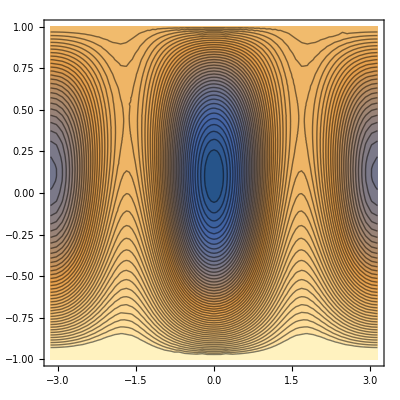

```mathematica
ContourPlot[hh/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07},{Φ, -π,π},{J, -1, 1},Contours->50]
```

```mathematica
sol=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->1,Cos[2Φ]->1},J]];
sol1=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-f/(2 f1 √(II^2-J^2)),Cos[2Φ]->-1+f^2/(2 f1^2 (II^2-J^2))},J]]
```

{J→(-II p R+II r R-4 δ)/((p-2 q+r) R)}

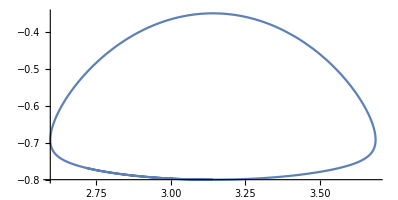

```mathematica
ploti=Flatten[NDSolve[{- 1/2 (f √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]==J'[t],1/4 (II p-II r+J[t] (2 f1+p-2 q+r)+(4 δ)/R+(2 f J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+2 f1 J[t] Cos[2 Φ[t]])==Φ'[t],J[0]==-.8,Φ[0]==π}/.{II->1,f->0.98, f1->.9,R->2,p->1.7,q->-1,r->-.4, δ->.2},{J[t],Φ[t]},{t,0,40}]];
ParametricPlot[{Φ[t]/.ploti[[2]],J[t]/.ploti[[1]]},{t,0,40}]
```

```mathematica
Cos[1.37]
```

0.19945

```mathematica
Sin[1.37]
```

0.979908

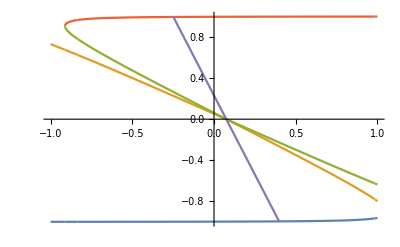

```mathematica
solPlot=sol/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
solPlot1=sol1/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
Jplot={J/.{solPlot[[1]]},J/.{solPlot[[2]]},J/.{solPlot[[3]]},J/.{solPlot[[4]]}};
Jplot1={J/.{solPlot1[[1]]}};
Plot[{Jplot,Jplot1},{δ,-1,1},PlotRange->{-1,1}]
```

```mathematica
Jplot/.{δ->-0.7}
```

{-0.998867-2.06595×10^-19 ⅈ,0.536878+1.34627×10^-17 ⅈ,0.649347-1.67795×10^-17 ⅈ,0.982453+3.52331×10^-18 ⅈ}

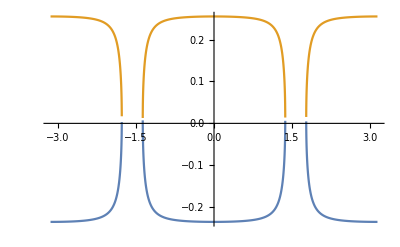

```mathematica
Plot[δplot,{Φ,-π,π}]
```

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→-0.943957-9.33782×10^-19 ⅈ,J→0.142438+1.47905×10^-17 ⅈ,J→0.348935-1.75238×10^-17 ⅈ,J→0.852584+3.66707×10^-18 ⅈ}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→-0.860094,J→0.834837,J→16.0126-10.0061 ⅈ,J→16.0126+10.0061 ⅈ}

```mathematica
ΦΦ=FullSimplify[D[hh,{Φ,2}]]
```

1/2 f √((II-J) (II+J)) Cos[Φ]+f1 (II-J) (II+J) Cos[2 Φ]

```mathematica
JJ = FullSimplify[D[hh,{J,2}]]
```

1/4 (2 f1+p-2 q+r+(2 f II^2 Cos[Φ])/((II-J) (II+J))^(3/2)+2 f1 Cos[2 Φ])

```mathematica
ΦJ=FullSimplify[D[D[hh,Φ],J]]
```

-(f J Sin[Φ])/(2 √((II-J) (II+J)))-f1 J Sin[2 Φ]

```mathematica
ΦΦ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0756148

```mathematica
JJ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.241302

```mathematica
ΦΦ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0550497

```mathematica
JJ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.609426